# Метод на допирателните (Нютон)

Дадено е уравнението:
x^2 - 33sin(x + π/(p + 1)) - (p + 2q)= 0, където p и q са съответно предпоследната и последната цифра от факултетния ни номер.
x^2 - 33sin(x + π/7) - 20 = 0
1. Да се намери общия брой на корените на уравнението.
2. Да се локализира най-малкия реален корен в интервал [a, b].
3. Да се проверят условията за приложение на метода на допирателните (Нютон).
4. Да се определи началното приближение за итерационния процес по метода на допирателните (Нютон).
5. Да се изчисли корена по метода на допирателните с точност 0,0000000001. Представете таблица с изчисленията.
6. Да се провери колко итерации биха били необходими, ако се използва метода на разполовяването в същия интервал [a, b] за същата точност.
7. Да се направи сравнение кой метод е по-ефективен за избрания интервал.

```mathematica
f[x_] := x^2 - 33Sin[x + π/7] - 20
```

```mathematica
f[x]
```

-20+x^2-33 Sin[π/7+x]

## 1. Да се намери общия брой на корените на уравнението.

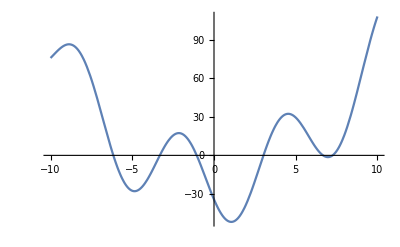

```mathematica
Plot[f[x], {x, -10, 10}]
```

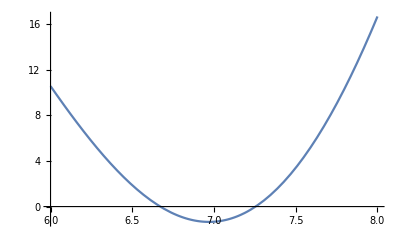

```mathematica
Plot[f[x], {x, 6, 8}]
```

Брой корени: 6

## 2. Да се локализира най-малкия реален корен в интервал [a, b].

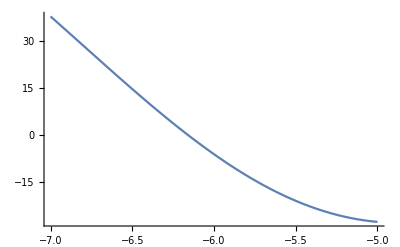

```mathematica
Plot[f[x], {x, -7, -5}]
```

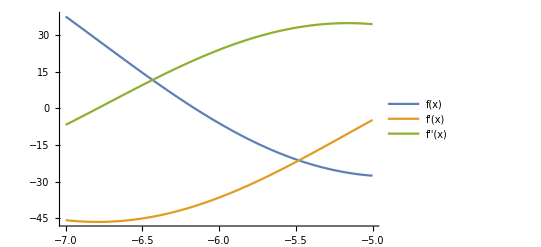

```mathematica
Plot[{f[x], f'[x], f''[x]}, {x, -7, -5}, PlotLegends->"Expressions"]
```

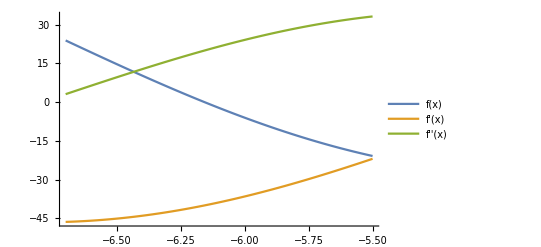

```mathematica
Plot[{f[x], f'[x], f''[x]}, {x, -6.7, -5.5}, PlotLegends->"Expressions"]
```

```mathematica
f[-6.7]
```

23.8347

```mathematica
f[-5.5]
```

-20.874

Извод:
1. f(-6.7) = 23.834.. > 0
2. f(-5.5) = -20.874... < 0
Следователно в двата края на функцията има различни знаци и функцията е непрекъсната в избрания интервал [-6.7;-5.5]. Следва, че функцията има поне един корен в дадения интервал.

## 3. Проверка на условията за сходимост

### Проверка на първата производна

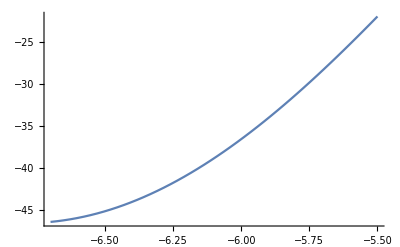

```mathematica
Plot[f'[x], {x, -6.7, -5.5}]
```

(1). Следва, че f’(x) има постоянен знак в дадения интервал.

### Проверка на втората производна

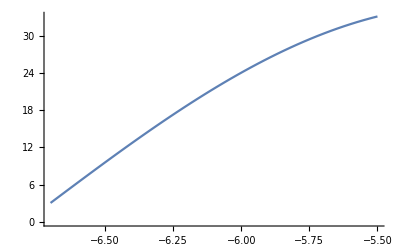

```mathematica
Plot[f''[x], {x, -6.7, -5.5}]
```

(1). Следва, че f’’(x) има постоянен знак в дадения интервал.

Извод: от (1) и (2) следва, че f'(x) и f''(x) са с постоянни знаци в разглеждания интервал [-6.7; -5.5] => Методът на допирателните е сходящ.

## 4. Избор на начално приближение

f(x_0) * f’’ > 0
=> f(x_0) < 0
=> x_0 = -5.5

### Пресмятане на постоянните величини:

```mathematica
Plot[Abs[f''[x]], {x, -6.7, -5.5}]
```

-Graphics-

От геометрични съображения максимума се достига в десния край на интервала, а минимума - в левия.

```mathematica
М2 = Abs[f''[-5.5]]
```

33.124

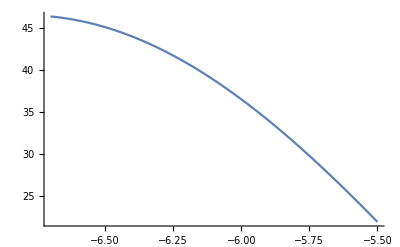

```mathematica
Plot[Abs[f'[x]], {x, -6.7, -5.5}]
```

От геометрични съображения максимума се достига в левия край на интервала, а минимума - в десния.

```mathematica
m1 = Abs[f'[-6.7]]
```

46.3831

```mathematica
p = М2/(2m1)
```

0.357069

## 5.Да се изчисли корена по метода на допирателните с точност 0,0000000001

```mathematica
f[x_]:=   x^2 - 33Sin[x + π/7] - 20
x0 = -5.5;
М2 = Abs[f''[-5.5]];
m1 = Abs[f'[-6.7]];
p = М2/(2m1);
epszad = 0.0000000001;
eps = 1;
Print["n = ",0,  " x_n = ", x0, " f(x) = ", f[x0], " f'(x) = ", f'[x0]];
For[n = 1, eps > epszad, n++,
x1 = x0 - f[x0]/f'[x0];
Print["n = ",n,  " x_n = ", x1, " f(x_n) = ", f[x1] " f'(x_n) = ", f'[x1], " ε_n = ", eps = p* (x1 - x0)^2];
x0 = x1
]
```

n = 0 x_n = -5.5 f(x) = -20.874 f'(x) = -21.9681

n = 1 x_n = -6.45019 f(x_n) = 12.4285  f'(x_n) = -44.5988 ε_n = 0.322386

n = 2 x_n = -6.17152 f(x_n) = 0.545566  f'(x_n) = -40.2943 ε_n = 0.0277295

n = 3 x_n = -6.15798 f(x_n) = 0.00180275  f'(x_n) = -40.0272 ε_n = 0.0000654573

n = 4 x_n = -6.15794 f(x_n) = 2.02026×10^-8  f'(x_n) = -40.0263 ε_n = 7.24292×10^-10

n = 5 x_n = -6.15794 f(x_n) = 1.42109×10^-14  f'(x_n) = -40.0263 ε_n = 9.0965×10^-20

## 6. Да се провери колко итерации биха били необходими, ако се използва метода на разполовяването в същия интервал [a, b] за същата точност

```mathematica
Log2[(-5.5 + 6.7)/0.0000000001] - 1
```

32.4823

## 6. Да се направи сравнение кой метод е по-ефективен за избрания интервал

Извод: По метода на допирателните (Нютон) биха били необходими 5 итерации за достигане на исканата точност. А по метода на разполовяването са необходими 32 итерации. Следователно методът на допирателните е по-ефективен за избрания интервал [-6.7, -5.5].